```mathematica
Nelinearni fit po "Modelu" :
```

```mathematica
Model=Po/2(1-Erf[(√2)/w h])
```

1/2 Po (1-Erf[(√2 h)/w])

```mathematica
<<NonlinearRegression`
```

General::obspkg: NonlinearRegression` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Ovdje se ubacuju podaci, parovi {visina u mikronima,snaga u mikrovatima}
```

```mathematica
podaci={{-75,55.9},{-50,52.7},{-25,21},{0,5},{25,1},{50,1},{75,1}}
```

{{-75,55.9},{-50,52.7},{-25,21},{0,5},{25,1},{50,1},{75,1}}

```mathematica
Nelinearna regresija izbacuje kao rezultat "w"<> i "Po"<> sa pripadnim greskama:
```

```mathematica
NonlinearRegress[podaci,Model,{{w,20},{Po,60}},h]
```

{BestFitParameters→{w→55.571,Po→43.9802},ParameterCITable→ | Estimate | Asymptotic SE | CI
w | 55.571 | 45.9535 | {-62.5561,173.698}
Po | 43.9802 | 8.49366 | {22.1465,65.8138},EstimatedVariance→162.691,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 2 | 5557.64 | 2778.82
Error | 5 | 813.457 | 162.691
Uncorrected Total | 7 | 6371.1 | 
Corrected Total | 6 | 3666.28 | ,AsymptoticCorrelationMatrix→(1. | 0.46382
0.46382 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 1.46758
Max Parameter-Effects | 0.766532
95. % Confidence Region | 0.415725}

```mathematica
Ponovo prilagodba za crtanje:
```

```mathematica
prilagodba=FindFit[podaci,Model,{{w,10},{Po,60}},h]
```

{w→55.571,Po→43.9802}

```mathematica
Crtani graf krivulje gaussijana i mjernih točaka:
```

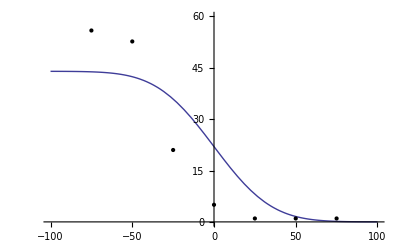

```mathematica
Plot[Evaluate[Model/.prilagodba],{h,-100,100},Epilog->Map[Point,podaci],PlotRange->{0,60}]
```